## Circle Of Least Confusion Notebook Section 1:

InterpolatingFunction::dmval: Input value {-0.000119392} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.000113337} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.93524×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

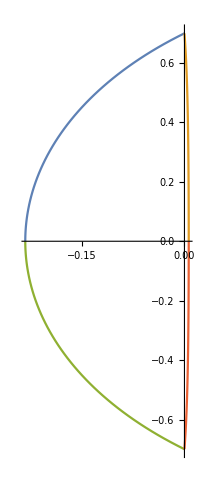

```mathematica
step = 0.05;
abimport = Import["C:\\Users\\Simon Hempel\\OneDrive - Carleton College\\Circle of Least Confusion Simulation\\ResultABk.xls"];
abtable = abimport[[1]];
aboutputy = abtable[[1;;10001;;20,{1,2}]];
aboutputx = abtable[[1;;10001;;20,{1,3}]];
acimport = Import["C:\\Users\\Simon Hempel\\OneDrive - Carleton College\\Circle of Least Confusion Simulation\\ResultACk.xls"];
actable = acimport[[1]];
acoutputy = actable[[1;;10001;;20,{1,2}]];
acoutputx = actable[[1;;10001;;20,{1,3}]];


acfunx = Interpolation[acoutputx];
acfuny = Interpolation[acoutputy];
rightrangecalc ={ FindMaximum[{acfuny[x], 0<x<.99}, {x,0.5}],FindMinimum[{acfuny[x], 0<x<.99}, {x,0.5}]};
rightrangemax= rightrangecalc[[1,1]];
rightrangemin = rightrangecalc[[2,1]];

abfunx = Interpolation[aboutputx];
abfuny = Interpolation[aboutputy];
leftrangecalc ={ FindMaximum[{abfuny[x], 0.01<x<.99}, {x,0.5}],FindMinimum[{abfuny[x], 0.01<x<.99}, {x,0.5}]};
leftrangemax= leftrangecalc[[1,1]];
leftrangemin = leftrangecalc[[2,1]];
ly = Table[y,{y,leftrangemin,leftrangemax,step}];
leftsidetable = abtable[[1;;10001;;20,{2,3}]];
rightsidetable = actable[[1;;10001;;20,{2,3}]];
leftfun = Interpolation[leftsidetable];
rightfun = Interpolation[rightsidetable];


lensfig=ParametricPlot[{{x = abfunx[t], y = abfuny[t]},{x = acfunx[t], y = acfuny[t]},{x = abfunx[t], y = -abfuny[t]},{x = acfunx[t], y = -acfuny[t]}},{t,0,1},AspectRatio->Automatic];
Show[lensfig]
```

## Defining Functions to Compute path Rays

```mathematica
lnorvec[yval_]:=Normalize[RotationMatrix[Pi/2].{leftfun'[yval],1}];
rnorvec[yval_]:=Normalize[RotationMatrix[Pi/2].{rightfun'[yval],1}];
table = Table[rnorvec[i],{i,leftrangemin,leftrangemax, .01}];

invecleft = {-1,0};  

n1 = 1;
n2 = 1.1;


outvec[norvec_,invec_]:=
(
(* Change direction if necessary so that normal points in direction of incoming ray. *)

r = n1/n2;

c1 = Dot[(norvec),-invec];
c2= Sqrt[1-r^2(1-c1^2)];
If[Element[c2,Reals], ,Print[c1]];
r invec + (r c1 - c2)(-norvec)
);

outvec2[norvec_,invec_]:=
(
(* Change direction if necessary so that normal points in direction of incoming ray. *)

r = n2/n1;

c1 = Dot[(norvec),invec];
c2= Sqrt[1-r^2(1-c1^2)];
r invec + (r c1 - c2)(-norvec)
);
(* Finds the t value where ray intersects the right lens interface. *)
findrightintersection[yval_]:=
(
startpnt = {leftfun[yval],yval};
outdir = outvec[lnorvec[yval],invecleft];
rayx[t_]=(startpnt+t*outdir)[[1]];
rayy[t_]=(startpnt+t*outdir)[[2]];
FindRoot[rayx[t]-rightfun[rayy[t]],{t,0}]
)
findleftintersection[yval_]:=
(
FindRoot[yval-leftfun[t],{t,0}]
)
(* Finds the point where ray from left interface intersects the right lens interface. *)
findintersectionpoint[yval_]:={leftfun[yval],yval}+t*outvec[lnorvec[yval],invecleft]/.findrightintersection[yval];
(* Finds the point where ray from left interface intersects the right lens interface. *)
findleftoutray[yval_]:={leftfun[yval],yval}+t*outvec[lnorvec[yval],invecleft];


findrightoutray[yval_]:=
(
invecright=outvec[lnorvec[yval],invecleft];
rightintersection = findintersectionpoint[yval];
outvecright = outvec2[rnorvec[rightintersection[[2]]],invecright];
 rightintersection+t*outvecright

);
circleofconfusion[xval_]:=
(
(* Table of y values at given xval for outgoing right interface rays. *)
topoutray = findrightoutray[leftrangemax];
toptstop = FindRoot[outray[[1]]==xval,{t,1}];
topvectorval = -(outray[[2]]/.toptstop);
allyvals=Table[
outray=findrightoutray[yval];
tstop = FindRoot[outray[[1]]==xval,{t,1}];
outray[[2]]/.tstop,
{yval,leftrangemin,leftrangemax,step}];
topvectorval-Max[allyvals]
);
(* Find the circle of LEAST confusion, looking in a given range xmin, xmax. The regular function FindArgMin is not giving accurate results here, so this is a stopgap.  *)
circleofleastconfusion[xmin_,xmax_]:=
(
delx=100;
colcxval = xmin;
step = (xmax-xmin)/delx;
While[circleofconfusion[colcxval]<0,colcxval;colcxval += step];
colcxval

)
```

## Visualization

Part::partd: Part specification outray⟦1⟧ is longer than depth of object.

FindRoot::nlnum: The function value {outray⟦1⟧} is not a list of numbers with dimensions {1} at {t} = {1.}.

Part::partd: Part specification outray⟦2⟧ is longer than depth of object.

FindRoot::nlnum: The function value {outray⟦1⟧} is not a list of numbers with dimensions {1} at {t} = {1.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[outray⟦1⟧==0,{t,1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1.505

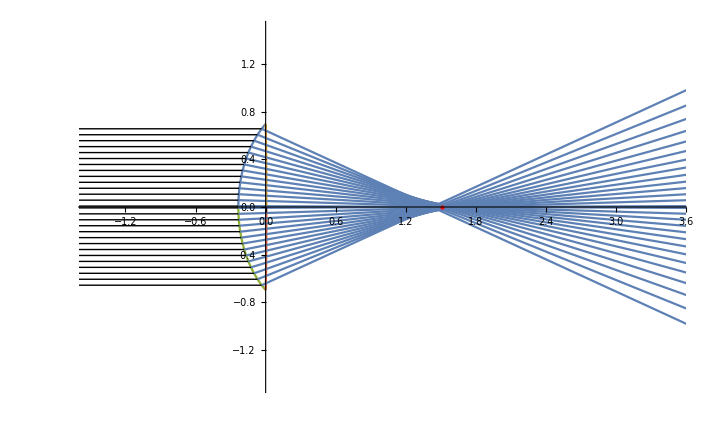

```mathematica
leftlinestop=Graphics[Table[Line[{{-2,k},{leftfun[k],k}}],{k,leftrangemin, leftrangemax, step}]];
leftlinesbottom=Graphics[Table[Line[{{-2,-k},{leftfun[k],-k}}],{k,leftrangemin, leftrangemax, step}]];
midlinestop = Table[ParametricPlot[{leftfun[yval],yval}+t*outvec[lnorvec[yval],invecleft],{t,0,t/.findrightintersection[yval]}],{yval,leftrangemin,leftrangemax,step}];
midlinesbottom = Table[ParametricPlot[{leftfun[yval],-yval}+t*ReflectionMatrix[{0,1}].outvec[lnorvec[yval],invecleft],{t,0,t/.findrightintersection[yval]}],{yval,leftrangemin,leftrangemax,step}];
rightlinestop=Table[
rray[t_]=findrightoutray[yval];
ParametricPlot[rray[t],{t,0,-20}],{yval,leftrangemin,leftrangemax,step}];
rightlinesbottom=Table[
rray[t_]=ReflectionMatrix[{0,1}].findrightoutray[yval];
ParametricPlot[rray[t],{t,0,-20}],{yval,leftrangemin,leftrangemax,step}];
colx = circleofleastconfusion[0,3.5];
Print[colx];
colcpoint = {colx, 0};
Show[lensfig,leftlinestop,leftlinesbottom,midlinesbottom, midlinestop,rightlinestop, rightlinesbottom,Graphics[{PointSize[Large],Red,Point[colcpoint]}],PlotRange->{{-1.5,3.5},{-1.5,1.5}}]
```